```mathematica
str = {{(0.02155246+0j),(-0.43499186-0.861860152j),(-0.00259418-0.00518671509j),(-0.15505308+0.208421608j)},{(-0.25933126-0.0151102401j),(-0.00230745-0.00532047478j),(-0.38089987-0.887094202j),(0.01384837-0.0165145803j)},{(0.00217941+0.00537419414j),(0.17092147-0.195619205j),(-0.01423979+0.0161782921j),(0.93435336+0.242908681j)},{(-0.41423272+0.872027575j),(-0.02154629+0.000516003926j),(0.25971754-0.00527500651j),(0.00271762+0.00512311911j)}}
```

{{0.0215525,-0.434992-0.86186 j,-0.00259418-0.00518672 j,-0.155053+0.208422 j},{-0.259331-0.0151102 j,-0.00230745-0.00532047 j,-0.3809-0.887094 j,0.0138484-0.0165146 j},{0.00217941+0.00537419 j,0.170921-0.195619 j,-0.0142398+0.0161783 j,0.934353+0.242909 j},{-0.414233+0.872028 j,-0.0215463+0.000516004 j,0.259718-0.00527501 j,0.00271762+0.00512312 j}}

```mathematica
StringReplace[ToString@str,{"j"->"ⅈ"}]
```

```mathematica
A= I*MatrixLog[{{0.0215525, -0.434992 - 0.86186 ⅈ, -0.00259418 - 0.00518672 ⅈ, -0.155053 + 0.208422 ⅈ}, {-0.259331 - 0.0151102 ⅈ, -0.00230745 - 0.00532047 ⅈ, -0.3809 - 0.887094 ⅈ, 0.0138484 - 0.0165146 ⅈ}, {0.00217941 + 0.00537419 ⅈ, 0.170921 - 0.195619 ⅈ, -0.0142398 + 0.0161783 ⅈ, 0.934353 + 0.242909 ⅈ}, {-0.414233 + 0.872028 ⅈ, -0.0215463 + 0.000516004 ⅈ, 0.259718 - 0.00527501 ⅈ, 0.00271762 + 0.00512312 ⅈ}}]
```

{{-0.312354+6.53979×10^-7 ⅈ,0.650164-0.484872 ⅈ,0.77356-0.0130073 ⅈ,-1.32133+0.0325291 ⅈ},{0.650164+0.484873 ⅈ,-0.172548-1.50858×10^-7 ⅈ,1.04539-0.845356 ⅈ,-0.515442+0.57218 ⅈ},{0.77356+0.0130072 ⅈ,1.04539+0.845355 ⅈ,-0.400517-6.31995×10^-7 ⅈ,0.212565+0.80506 ⅈ},{-1.32133-0.0325288 ⅈ,-0.515442-0.572181 ⅈ,0.212566-0.805059 ⅈ,-0.510204+1.57819×10^-7 ⅈ}}

```mathematica
func[x_]:=If[Abs[x]>0.01,1,0];
B=Map[func,A,{2}]
```

{{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,1,1}}

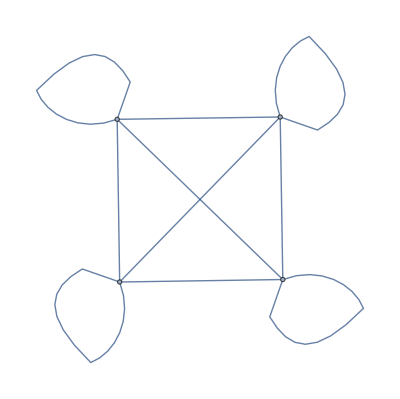

```mathematica
AdjacencyGraph[B]
```

```mathematica
str = {{(0.29307558+0j),(0.93362963-0.205916844j),(0.0016278-0.000918337403j),(0.00454035-0.00406918714j)},{(-0.00502272-0.0034562003j),(0.00173173+0.000702993291j),(0.95227923+0.0850312627j),(-0.2906771+0.0374181821j)},{(-0.00116031+0.00146518593j),(-0.00266687+0.00548277873j),(0.04557732-0.289509935j),(-0.05821924-0.954293749j)},{(0.06409588+0.95391706j),(-0.08216726-0.281321588j),(0.00334505+0.00509741831j),(-0.00133788-0.00130505337j)}}
```

{{0.293076,0.93363-0.205917 j,0.0016278-0.000918337 j,0.00454035-0.00406919 j},{-0.00502272-0.0034562 j,0.00173173+0.000702993 j,0.952279+0.0850313 j,-0.290677+0.0374182 j},{-0.00116031+0.00146519 j,-0.00266687+0.00548278 j,0.0455773-0.28951 j,-0.0582192-0.954294 j},{0.0640959+0.953917 j,-0.0821673-0.281322 j,0.00334505+0.00509742 j,-0.00133788-0.00130505 j}}

```mathematica
StringReplace[ToString@str,{"j"->"ⅈ"}]
```

```mathematica
A= I*MatrixLog[{{0.293076, 0.93363 - 0.205917 ⅈ, 0.0016278 - 0.000918337 ⅈ, 0.00454035 - 0.00406919 ⅈ}, {-0.00502272 - 0.0034562 ⅈ, 0.00173173 + 0.000702993 ⅈ, 0.952279 + 0.0850313 ⅈ, -0.290677 + 0.0374182 ⅈ}, {-0.00116031 + 0.00146519 ⅈ, -0.00266687 + 0.00548278 ⅈ, 0.0455773 - 0.28951 ⅈ, -0.0582192 - 0.954294 ⅈ}, {0.0640959 + 0.953917 ⅈ, -0.0821673 - 0.281322 ⅈ, 0.00334505 + 0.00509742 ⅈ, -0.00133788 - 0.00130505 ⅈ}}]
```

{{0.47935+1.49499×10^-7 ⅈ,-0.493488+0.838723 ⅈ,0.531014+0.0031764 ⅈ,-0.754714+0.623669 ⅈ},{-0.493488-0.838722 ⅈ,0.880945+1.25015×10^-7 ⅈ,-0.829309+0.46704 ⅈ,0.524356-0.902755 ⅈ},{0.531014-0.00317641 ⅈ,-0.829309-0.467041 ⅈ,1.13901+1.70406×10^-7 ⅈ,0.575314+0.75092 ⅈ},{-0.754714-0.623668 ⅈ,0.524356+0.902755 ⅈ,0.575314-0.75092 ⅈ,0.898333+1.32185×10^-7 ⅈ}}

```mathematica
func[x_]:=If[Abs[x]>0.01,1,0];
B=Map[func,A,{2}]
```

{{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,1,1}}

```mathematica
AdjacencyGraph[B]
```

-Graphics-